```mathematica
(*
Setup data and reference roots
*)
nbPath=NotebookDirectory[];
nbDepth=FileNameDepth[nbPath];
quiccroot=FileNameJoin[FileNameSplit[nbPath][[1;;nbDepth-4]]];
dataroot=FileNameJoin[Flatten[{quiccroot,"build","Components","Transform","TestSuite"}]];
dataroot::wrongpath="Path to data root does not exist: `1`";
If[!DirectoryQ[dataroot],
Message[dataroot::wrongpath,dataroot];
Abort[];
];

Hyperlink["Energy Tests",{SelectedNotebook[],"energyTests"}]
Hyperlink["Projector Tests",{SelectedNotebook[],"projectorTests"}]
Hyperlink["Integrator Tests",{SelectedNotebook[],"integratorTests"}]
Hyperlink["Backward-Forward loop Tests",{SelectedNotebook[],"bfloopTests"}]
Hyperlink["Power Tests",{SelectedNotebook[],"powerTests"}]
Hyperlink["Radial Power Tests",{SelectedNotebook[],"radialPowerTests"}]
```

Energy Testsb4a0dd8d-8a96-431c-a322-50aa4054eb68energyTestsButtonData

Projector Testsb4a0dd8d-8a96-431c-a322-50aa4054eb68projectorTestsButtonData

Integrator Testsb4a0dd8d-8a96-431c-a322-50aa4054eb68integratorTestsButtonData

Backward-Forward loop Testsb4a0dd8d-8a96-431c-a322-50aa4054eb68bfloopTestsButtonData

Power Testsb4a0dd8d-8a96-431c-a322-50aa4054eb68powerTestsButtonData

Radial Power Testsb4a0dd8d-8a96-431c-a322-50aa4054eb68radialPowerTestsButtonData

```mathematica
(* 
General Worland setup
*)
(*Worland package setup*)
pkgroot=FileNameJoin[Flatten[{quiccroot,"Components","TestSuite","Mathematica"}]];
AppendTo[$Path, pkgroot];
Worland`$mpprec=100;
Worland`$WorlandType="SphEnergy";
Needs["Worland`"];
ParallelNeeds["Worland`"]
$MaxExtraPrecision=1000;
mpprec = Worland`$mpprec;

(*FDSphere package*)
Needs["FDSphere`"];

datadir={"_data","Transform","FiniteDiff","Sphere"};
refdir={"_refdata","Transform","FiniteDiff","Sphere"};

(*intgdivrdrWorland*)
divr[f_,l_,t_]:=Module[{out},
out = Simplify[1/t f];
out]
divrdr[f_,l_,t_]:=Module[{out},
out = Simplify[1/t D[t f,t]];
out]
(* 
Operators to work on grid
*)
WnlEnergy[n_,l_,r_]:=r^l JacobiP[n,$wsphα,l+$wsphdβ,2 r^2-1]/norm[n,$wsphα,l+$wsphdβ]
divrWnlzeroWnl[n_,l_,r_]:= If[l==0,0r,divrWnl[n,l,r]];
dWnlWnl[n_,l_,r_]:= If[l==0,Wnl[n,l,r],dWnl[n,l,r]];
divrdrWnlzeroWnl[n_,l_,r_]:= If[l==0,0r,divrdrWnl[n,l,r]];

uniformRadialGrid[n_]:=N[Table[i/(n-1),{i,0,n-1}],mpprec]

uniformTruncation[maxN_,l_]:=maxN;
dealiasGrid[n_,l_,tFunc_:uniformTruncation]:=Floor[3(tFunc[n,l]+l/2+8)/2];
uniformSetup[maxL_]:=Module[{nN,nR,f},
f=uniformTruncation;
nN=Floor[maxL/2]+1;
nR=dealiasGrid[nN-1,maxL,f];
{nN,nR,f}
];

(*
Tools for generating spectral space spectra 
*)
unitSpectrum[n_,maxN_,l_,tFunc_:uniformTruncation]:=If[n<=tFunc[maxN,l],1,0];
maxSpectrum[n_,maxN_,l_,tFunc_:uniformTruncation]:=If[n==tFunc[maxN,l],1,0];
minSpectrum[n_,maxN_,l_,tFunc_:uniformTruncation]:=If[n==0,1,0];
randSpectrum[n_,maxN_,l_,tFunc_:uniformTruncation]:=Module[{val},
If[n<=tFunc[maxN,l],
val =N[ IntegerPart[RandomReal[{1/10,1}] 10^3]/10^3,mpprec];,
val=0];
val
]
(*
Configure which output to generate
*)
genInDataDefault=False;
genRefDataDefault=False;
generateInData=genInDataDefault;
generateRefData=genRefDataDefault;
configureGenerator[genIn_:genInDataDefault,genRef_:genRefDataDefault]:=
Module[{},
generateInData=genIn;
generateRefData=genRef;
];
(*
Generate metadata
*)
createMetadata[nN_, gridN_,ls_, tFunc_]:=Module[{descr,lModes,mModes,nL=Length@ls,header },
lModes=Flatten[Table[{ls[[i]],1},{i,1,nL}]];
mModes=Flatten[Table[{0,tFunc[gridN-1,ls[[i]]]+1},{i,1,nL}]];;
header={
"# Format description",
"# line 1: number of lines",
"# line 2: simulation modal size", 
"# line 3: simulation physical size", 
"# line 4: number of modes nK", 
"# line 5 + 2*k: mode",
"# line 6 + 2*k: number of 2D modes",
"# line (5 + 2*nK) + 2*j: 2D mode",
"# line (6 + 2*nK) + 2*j: number of 1D modes"
};
descr = Flatten[{gridN,gridN,nL,lModes,mModes}];
descr = Prepend[descr,Length@descr];
descr = Flatten[Prepend[descr,header]];
descr
];
```

Worland:: Using SphEnergy Worland type

Worland:: Number of digits is set to 100

$mpprec::shdw: Symbol $mpprec appears in multiple contexts {FDSphere`,Worland`}; definitions in context FDSphere` may shadow or be shadowed by other definitions.

Energy tests

```mathematica
testEnergy[meta_,id_,infunc_,gfunc_,opfunc_,name_,OptionsPattern[]]:=
Module[{outprec = 32,i,tmp,nN,gridN,ls,descr, specR,grid,zg ,in,inI,inR,gq,xLeg,wLeg,rLeg,ref,msg,tempmsg,fbase,fname,tFunc=OptionValue[truncationFunc]},
nN=meta[[1]];
gridN = meta[[2]];
ls=meta[[3]];
fbase=name<>"_id"<>ToString[id];
msg="Exporting "<>name<>" FD sphere operator for N = "<>ToString[nN]<>", Ng = " <>ToString[gridN]<>", l = "<>ToString[ls]<>"...";
(* Generate meta data *)
fname=fbase<>"_meta.dat";
descr=createMetadata[gridN,gridN,ls,tFunc];
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],descr];
(* Generate input data *)
If[generateInData,
specR=ParallelTable[infunc[i-1,nN-1,ls[[j]],tFunc],{i,1,nN},{j,1,Length@ls}];
grid = gfunc[gridN];
zg = 0grid;
inR=Table[Sum[If[specR[[i,j]]!=0,tmp=Wnl[i-1,ls[[j]],ζ];tmp=tmp/.{ζ->grid};If[Length@tmp < Length@grid,tmp=Table[tmp,Length@grid]];specR[[i,j]]tmp,zg],{i,1,nN}],{j,1,Length@ls}];
inI = -inR;
in = Join[Transpose[inR],Transpose[inI]];
in=N[in,outprec];
fname=fbase<>"_in.dat";
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],in,"Table"];
];
(* Generate output referece *)
If[generateInData&&generateRefData,
gq=GaussianQuadratureWeights[4nN+2ls[[-1]]+4,-1,1,mpprec];
xLeg=gq[[;;,1]];wLeg=gq[[;;,2]];rLeg=(xLeg+1)/2;
ref=Table[specR=infunc[i-1,nN-1,ls[[j]],tFunc];tmp=Sum[(specR-specR ⅈ)opfunc[i-1,ls[[j]],rLeg],{i,1,nN}];Chop[1/2 Dot[wLeg,(rLeg^2 Abs[tmp]^2)]],{j,1,Length@ls}];
ref=N[ref,outprec];
fname=fbase<>"_ref.dat";
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],ref];
];
Print[Row[{msg,Style[" Done("<>DateString[]<>")",FontColor->Green]}]];
];
Options[testEnergy]={truncationFunc->uniformTruncation};
```

```mathematica
generateEnergies[meta_,tId_,inOp_,gfunc_,OptionsPattern[]]:=Module[{tFunc=OptionValue[truncationFunc]},
configureGenerator[OptionValue[genIn],OptionValue[genRef]];
testEnergy[meta,tId,inOp,gfunc,Wnl,"Reductor/EnergyR2",truncationFunc->tFunc];
testEnergy[meta,tId,inOp,gfunc,divrWnlzeroWnl,"Reductor/Energy",truncationFunc->tFunc];
testEnergy[meta,tId,inOp,gfunc,divrdrWnlzeroWnl,"Reductor/EnergyD1R1",truncationFunc->tFunc];
testEnergy[meta,tId,inOp,gfunc,slaplWnl,"Reductor/EnergySLaplR2",truncationFunc->tFunc];
];
Options[generateEnergies]={truncationFunc->uniformTruncation,genIn->False, genRef->False};
```

```mathematica
maxL=18;
genTags={True,True};
spectra={minSpectrum,maxSpectrum,unitSpectrum,randSpectrum};
For[it=1,it<= Length[spectra],it++,
Print[StringRepeat["%",50]];
id=(it-1);
Print["%%% Generating data with "<>ToString[spectra[[it]]]<>" spectrum, id = "<>ToString[id]];
{nN,nR,tFunc}=uniformSetup[maxL];
meta = {nN,nR, {1,2,3,8,maxL}};
generateEnergies[meta,id,spectra[[it]],uniformRadialGrid,truncationFunc->tFunc, genIn->genTags[[1]], genRef->genTags[[2]]];
];
Clear[it,spectra,is,maxL,nN,nR,tFunc,meta,id]
```

%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%

%%% Generating data with minSpectrum spectrum, id = 0

Exporting Reductor/EnergyR2 FD sphere operator for N = 10, Ng = 39, l = {1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 11:00:25)

Exporting Reductor/Energy FD sphere operator for N = 10, Ng = 39, l = {1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 11:00:25)

Exporting Reductor/EnergyD1R1 FD sphere operator for N = 10, Ng = 39, l = {1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 11:00:25)

Exporting Reductor/EnergySLaplR2 FD sphere operator for N = 10, Ng = 39, l = {1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 11:00:25)

%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%

%%% Generating data with maxSpectrum spectrum, id = 1

Exporting Reductor/EnergyR2 FD sphere operator for N = 10, Ng = 39, l = {1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 11:00:26)

Exporting Reductor/Energy FD sphere operator for N = 10, Ng = 39, l = {1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 11:00:26)

Exporting Reductor/EnergyD1R1 FD sphere operator for N = 10, Ng = 39, l = {1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 11:00:26)

Exporting Reductor/EnergySLaplR2 FD sphere operator for N = 10, Ng = 39, l = {1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 11:00:26)

%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%

%%% Generating data with unitSpectrum spectrum, id = 2

Exporting Reductor/EnergyR2 FD sphere operator for N = 10, Ng = 39, l = {1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 11:00:27)

Exporting Reductor/Energy FD sphere operator for N = 10, Ng = 39, l = {1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 11:00:27)

Exporting Reductor/EnergyD1R1 FD sphere operator for N = 10, Ng = 39, l = {1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 11:00:27)

Exporting Reductor/EnergySLaplR2 FD sphere operator for N = 10, Ng = 39, l = {1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 11:00:28)

%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%

%%% Generating data with randSpectrum spectrum, id = 3

Exporting Reductor/EnergyR2 FD sphere operator for N = 10, Ng = 39, l = {1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 11:00:28)

Exporting Reductor/Energy FD sphere operator for N = 10, Ng = 39, l = {1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 11:00:28)

Exporting Reductor/EnergyD1R1 FD sphere operator for N = 10, Ng = 39, l = {1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 11:00:29)

Exporting Reductor/EnergySLaplR2 FD sphere operator for N = 10, Ng = 39, l = {1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 11:00:29)

```mathematica
genTags={True,True};
spectra={randSpectrum};
For[it=1,it<= Length[spectra],it++,
Print[StringRepeat["%",50]];
For[ p = 4,p<9,p++,
id=100it+p;
Print["%%% Generating data with "<>ToString[spectra[[it]]]<>" spectrum, id = "<>ToString[id]];
maxL=2^p-1;
{nN,nR,tFunc}=uniformSetup[maxL];
meta={nN,nR,Table[l,{l,0,maxL}]};
generateEnergies[meta,id,spectra[[it]],,uniformRadialGrid,truncationFunc->tFunc,genIn->genTags[[1]],genRef->genTags[[2]]];
Clear[nL,nN,nR,tFunc,meta];
];
];
Clear[it,spectra,is,maxL,nN,nR,tFunc,meta,id,genTags]
```

Projector tests

```mathematica
testProjector[meta_,id_,infunc_,gfunc_,opfunc_,name_,OptionsPattern[]]:=
Module[{outprec = 32,i,nN,gridN,ls,descr, specR,in,inR,inI,grid,zg,ref,refR,refI,fdOp,msg,tempmsg,fbase,fname,tFunc=OptionValue[truncationFunc]},
nN=meta[[1]];
gridN = meta[[2]];
ls=meta[[3]];
fbase=name<>"_id"<>ToString[id];
msg="Exporting "<>name<>" FD sphere operator for N = "<>ToString[nN]<>", Ng = " <>ToString[gridN]<>", l = "<>ToString[ls]<>"...";
(* Generate meta data *)
fname=fbase<>"_meta.dat";
descr=createMetadata[nN,gridN,ls,tFunc];
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],descr];
(* Generate input data *)
If[generateInData,
specR=ParallelTable[infunc[i-1,nN-1,ls[[j]],tFunc],{i,1,nN},{j,1,Length@ls}];
grid = gfunc[gridN];
zg = 0grid;
inR=Table[Sum[If[specR[[i,j]]!=0,tmp=Wnl[i-1,ls[[j]],ζ];tmp=tmp/.{ζ->grid};If[Length@tmp < Length@grid,tmp=Table[tmp,Length@grid]];specR[[i,j]]tmp,zg],{i,1,nN}],{j,1,Length@ls}];
inI = -inR;
in = Join[Transpose[inR],Transpose[inI]];
in=N[in,outprec];
fname=fbase<>"_in.dat";
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],in,"Table"];
];
(* Generate reference data *)
If[generateInData&&generateRefData,
refR=Table[opfunc[grid, ls[[j]]].Transpose[inR][[;;,j]],{j,1,Length@ls}];
refI=-refR;
ref=Join[Transpose[refR],Transpose[refI]];
ref=N[ref,outprec];
fname=fbase<>"_ref.dat";
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],ref,"Table"];
];
Print[Row[{msg,Style[" Done("<>DateString[]<>")",FontColor->Green]}]];
];
Options[testProjector]={truncationFunc->uniformTruncation};
```

```mathematica
generateProjectors[meta_,tId_,inOp_,gfunc_,OptionsPattern[]]:=Module[{subdir,tFunc=OptionValue[truncationFunc]},
configureGenerator[OptionValue[genIn],OptionValue[genRef]];

(* PROJECTRORS *)
subdir="Projector/";
testProjector[meta,tId,inOp,gfunc,fdsphproj,subdir<>"P",truncationFunc->tFunc];
testProjector[meta,tId,inOp,gfunc,fdsphr1,subdir<>"R1",truncationFunc->tFunc];
testProjector[meta,tId,inOp,gfunc,fdsphdivr1,subdir<>"DivR1",truncationFunc->tFunc];
testProjector[meta,tId,inOp,gfunc,fdsphd1,subdir<>"D1",truncationFunc->tFunc];
testProjector[meta,tId,inOp,gfunc,fdsphd2,subdir<>"D2",truncationFunc->tFunc];
testProjector[meta,tId,inOp,gfunc,fdsphd3,subdir<>"D3",truncationFunc->tFunc];
testProjector[meta,tId,inOp,gfunc,fdsphd4,subdir<>"D4",truncationFunc->tFunc];
testProjector[meta,tId,inOp,gfunc,fdsphdivr1d1r1,subdir<>"DivR1D1R1",truncationFunc->tFunc];
testProjector[meta,tId,inOp,gfunc,fdsphlapl,subdir<>"SphLapl",truncationFunc->tFunc];

testProjector[meta,tId,inOp,gfunc,fdsphzerol0[fdsphr1],subdir<>"R1_Zero",truncationFunc->tFunc];
testProjector[meta,tId,inOp,gfunc,fdsphzerol0[fdsphdivr1],subdir<>"DivR1_Zero",truncationFunc->tFunc];
testProjector[meta,tId,inOp,gfunc,fdsphzerol0[fdsphdivr1d1r1],subdir<>"DivR1D1R1_Zero",truncationFunc->tFunc];

(* INTEGRATORS *)
subdir="Integrator/";
testProjector[meta,tId,inOp,gfunc,fdsphproj,subdir<>"P",truncationFunc->tFunc];
testProjector[meta,tId,inOp,gfunc,fdsphzerol0[fdsphproj],subdir<>"P_Zero",truncationFunc->tFunc];
testProjector[meta,tId,inOp,gfunc,fdsphzerol0[fdsphr1],subdir<>"R1_Zero",truncationFunc->tFunc];
testProjector[meta,tId,inOp,gfunc,fdsphzerol0[fdsphdivr1],subdir<>"DivR1_Zero",truncationFunc->tFunc];
testProjector[meta,tId,inOp,gfunc,fdsphzerol0[fdsphdivr1d1r1],subdir<>"DivR1D1R1_Zero",truncationFunc->tFunc];
];
Options[generateProjectors]={truncationFunc->uniformTruncation,genIn->False, genRef->False};
```

```mathematica
maxL=18;
genTags={True,True};
spectra={minSpectrum,maxSpectrum,unitSpectrum,randSpectrum};
For[it=1,it<= Length[spectra],it++,
id=(it-1);
Print[StringRepeat["%",50]];
Print["%%% Generating data with "<>ToString[spectra[[it]]]<>" spectrum, id = "<>ToString[id]];
{nN,nR,tFunc}=uniformSetup[maxL];
meta = {nN,nR, {0,1,2,3,8,maxL}};
generateProjectors[meta,id,spectra[[it]],fdsphgrid,truncationFunc->uniformTruncation, genIn->genTags[[1]], genRef->genTags[[2]]];
];
Clear[it,spectra,is,maxL,nN,nR,tFunc,meta,id,genTags]
```

%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%

%%% Generating data with minSpectrum spectrum, id = 0

Get::noopen: Cannot open Worland`.

Needs::nocont: Context Worland` was not created when Needs was evaluated.

Get::noopen: Cannot open Worland`.

Needs::nocont: Context Worland` was not created when Needs was evaluated.

Get::noopen: Cannot open Worland`.

Needs::nocont: Context Worland` was not created when Needs was evaluated.

Get::noopen: Cannot open Worland`.

Needs::nocont: Context Worland` was not created when Needs was evaluated.

Get::noopen: Cannot open Worland`.

Needs::nocont: Context Worland` was not created when Needs was evaluated.

Get::noopen: Cannot open Worland`.

Needs::nocont: Context Worland` was not created when Needs was evaluated.

Exporting Projector/P FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:14)

Exporting Projector/R1 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:14)

Exporting Projector/DivR1 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:14)

Exporting Projector/D1 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:15)

Exporting Projector/D2 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:15)

Exporting Projector/D3 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:15)

Exporting Projector/D4 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:16)

Exporting Projector/DivR1D1R1 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:16)

Exporting Projector/SphLapl FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:16)

Exporting Projector/R1_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:16)

Exporting Projector/DivR1_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:16)

Exporting Projector/DivR1D1R1_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:17)

Exporting Integrator/P FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:17)

Exporting Integrator/P_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:17)

Exporting Integrator/R1_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:17)

Exporting Integrator/DivR1_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:17)

Exporting Integrator/DivR1D1R1_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:18)

%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%

%%% Generating data with maxSpectrum spectrum, id = 1

Exporting Projector/P FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:18)

Exporting Projector/R1 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:18)

Exporting Projector/DivR1 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:18)

Exporting Projector/D1 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:18)

Exporting Projector/D2 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:19)

Exporting Projector/D3 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:19)

Exporting Projector/D4 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:19)

Exporting Projector/DivR1D1R1 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:19)

Exporting Projector/SphLapl FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:19)

Exporting Projector/R1_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:19)

Exporting Projector/DivR1_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:20)

Exporting Projector/DivR1D1R1_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:20)

Exporting Integrator/P FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:20)

Exporting Integrator/P_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:20)

Exporting Integrator/R1_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:20)

Exporting Integrator/DivR1_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:21)

Exporting Integrator/DivR1D1R1_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:21)

%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%

%%% Generating data with unitSpectrum spectrum, id = 2

Exporting Projector/P FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:21)

Exporting Projector/R1 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:21)

Exporting Projector/DivR1 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:21)

Exporting Projector/D1 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:22)

Exporting Projector/D2 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:22)

Exporting Projector/D3 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:22)

Exporting Projector/D4 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:22)

Exporting Projector/DivR1D1R1 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:22)

Exporting Projector/SphLapl FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:23)

Exporting Projector/R1_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:24)

Exporting Projector/DivR1_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:24)

Exporting Projector/DivR1D1R1_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:26)

Exporting Integrator/P FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:26)

Exporting Integrator/P_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:26)

Exporting Integrator/R1_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:27)

Exporting Integrator/DivR1_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:27)

Exporting Integrator/DivR1D1R1_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:28)

%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%

%%% Generating data with randSpectrum spectrum, id = 3

Exporting Projector/P FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:28)

Exporting Projector/R1 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:29)

Exporting Projector/DivR1 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:29)

Exporting Projector/D1 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:29)

Exporting Projector/D2 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:29)

Exporting Projector/D3 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:29)

Exporting Projector/D4 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:29)

Exporting Projector/DivR1D1R1 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:30)

Exporting Projector/SphLapl FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:32)

Exporting Projector/R1_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:32)

Exporting Projector/DivR1_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:32)

Exporting Projector/DivR1D1R1_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:33)

Exporting Integrator/P FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:33)

Exporting Integrator/P_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:33)

Exporting Integrator/R1_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:33)

Exporting Integrator/DivR1_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:33)

Exporting Integrator/DivR1D1R1_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Fri 5 Sep 2025 07:58:33)

```mathematica
generateDbProjectors[meta_,tId_,inOp_,gfunc_,OptionsPattern[]]:=Module[{subdir,tFunc=OptionValue[truncationFunc]},
configureGenerator[OptionValue[genIn],OptionValue[genRef]];
subdir="Projector/";
testProjector[meta,tId,inOp,gfunc,Wnl,subdir<>"P",truncationFunc->tFunc];
];
Options[generateDbProjectors]={truncationFunc->uniformTruncation,genIn->False,genRef->False};
```

```mathematica
genTags={True,True};
spectra={randSpectrum};
For[it=1,it<= Length[spectra],it++,
Print[StringRepeat["%",50]];
For[ p = 4,p<7,p++,
id=100it+p;
Print["%%% Generating data with "<>ToString[spectra[[it]]]<>" spectrum], id = "<>ToString[id]];
maxL=2^p-1;
{nN,nR,tFunc}=uniformSetup[maxL];
meta={nN,nR,Table[l,{l,0,maxL}]};
generateDbProjectors[meta,id,spectra[[it]],wgrid,truncationFunc->tFunc,genIn->genTags[[1]],genRef->genTags[[2]]];
Clear[nL,nN,nR,tFunc,meta];
];
];
Clear[it,spectra,is,maxL,nN,nR,tFunc,meta,id,genTags]
```

Backward-Forward loop tests

```mathematica
testBFLoop[meta_,id_,infunc_,gfunc_,wfunc_,bopfunc_,fopfunc_,name_,OptionsPattern[]]:=
Module[{outprec = 32,i,nN,gridN,ls,descr, in,inR,inI,grid,wgts,tmpR,tmpI,ref,refR,refI,msg,tempmsg,fbase,fname,tFunc=OptionValue[truncationFunc]},
nN=meta[[1]];
gridN = meta[[2]];
ls=meta[[3]];
fbase=name<>"_id"<>ToString[id];
msg="Exporting "<>name<>" Worland operator for N = "<>ToString[nN]<>", Ng = " <>ToString[gridN]<>", l = "<>ToString[ls]<>"...";
(* Generate meta data *)
fname=fbase<>"_meta.dat";
descr=createMetadata[nN,gridN,ls,tFunc];
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],descr];
(* Generate input data *)
If[generateInData,
inR=ParallelTable[infunc[i-1,nN-1,ls[[j]],tFunc],{i,1,nN},{j,1,Length@ls}];
inI=ParallelTable[-infunc[i-1,nN-1,ls[[j]],tFunc],{i,1,nN},{j,1,Length@ls}];
in = Join[inR,inI];
fname=fbase<>"_in.dat";
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],in,"Table"];
];
(* Generate reference data *)
If[generateInData&&generateRefData,
grid = gfunc[gridN];
tmpR=Table[Sum[inR[[i,j]]bopfunc[i-1,ls[[j]],grid],{i,1,nN}],{j,1,Length@ls}];
tmpI=Table[Sum[inI[[i,j]]bopfunc[i-1,ls[[j]],grid],{i,1,nN}],{j,1,Length@ls}];
grid = gfunc[gridN];
wgts=wfunc[gridN];
refR=Table[Dot[wgts fopfunc[i-1,ls[[j]],grid],Transpose[tmpR[[j,;;]]]],{i,1,nN},{j,1,Length@ls}];
refI=Table[Dot[wgts fopfunc[i-1,ls[[j]],grid],Transpose[tmpI[[j,;;]]]],{i,1,nN},{j,1,Length@ls}];
ref = Join[refR,refI];
ref = Chop[ref,10^(-mpprec+5)];
fname=fbase<>"_ref.dat";
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],ref,"Table"];
];
Print[Row[{msg,Style[" Done("<>DateString[]<>")",FontColor->Green]}]];
];
Options[testBFLoop]={truncationFunc->uniformTruncation};
```

```mathematica
generateBFLoops[meta_,tId_,inSpec_,gfunc_,wfunc_,OptionsPattern[]]:=Module[{tFunc=OptionValue[truncationFunc]},
configureGenerator[OptionValue[genIn],OptionValue[genRef]];
testBFLoop[meta,tId,inSpec,gfunc,wfunc,Wnl,Wnl,"BFLoop/P",truncationFunc->tFunc];;
];
Options[generateBFLoops]={truncationFunc->uniformTruncation,genIn->False,genRef->False};
```

```mathematica
maxL=18;
genTags={{True,True},{True,True}};
setups={uniformSetup,triangularSetup};
spectra={minSpectrum,maxSpectrum,unitSpectrum,randSpectrum};
For[it=1,it<= Length[spectra],it++,
Print[StringRepeat["%",50]];
Print["%%% Generating data with "<>ToString[spectra[[it]]]<>" spectrum"];
For[ is = 1,is<= Length[setups],is++,
{nN,nR,tFunc}=setups[[is]][maxL];
meta = {nN,nR, {1,2,3}};
id=1000(is-1)+(it-1);
Print["--- Generating data with "<>ToString[setups[[is]]]<>" truncation, id = "<>ToString[id]];
generateBFLoops[meta,id,spectra[[it]],wgrid,wweights,truncationFunc->tFunc, genIn->genTags[[is]][[1]], genRef->genTags[[is]][[2]]];
];
];
Clear[setups,it,spectra,is,k,maxL,nN,nR,tFunc,meta,id,genTags]
```

```mathematica
genTags={{False,False},{True,True}};
spectra={randSpectrum};
For[it=1,it<= Length[spectra],it++,
Print[StringRepeat["%",50]];
Print["%%% Generating data with "<>ToString[spectra[[it]]]<>" spectrum"];
For[ is = 1,is<= Length[setups],is++,
For[ p = 4,p<12,p++,
maxL=2^p-1;
{nN,nR,tFunc}=setups[[is]][maxL];
meta = {nN,nR, {1,2,3}};
id=1000(is-1)+100it+p;
Print["--- Generating data with "<>ToString[setups[[is]]]<>" truncation, id = "<>ToString[id]];
generateBFLoops[meta,id,spectra[[it]],wgrid,wweights,truncationFunc->tFunc, genIn->genTags[[is]][[1]], genRef->genTags[[is]][[2]]];
];
];
];
Clear[setups,it,spectra,is,k,maxL,p,nN,nR,tFunc,meta,id,genTags]
```

Power tests

```mathematica
testPower[meta_,id_,infunc_,gfunc_,wfunc_,bopfunc_,fopfunc_,name_,OptionsPattern[]]:=
Module[{outprec = 32,i,nN,gridN,ls,descr, in,inR,inI,grid,wgts,tmpR,tmpI,ref,refR,refI,msg,tempmsg,fbase,fname,lShift=OptionValue[lShift],tFunc=OptionValue[truncationFunc]},
nN=meta[[1]];
gridN = meta[[2]]+4;
ls=meta[[3]];
fbase=name<>"_id"<>ToString[id];
msg="Exporting "<>name<>" Worland operator for N = "<>ToString[nN]<>", Ng = " <>ToString[gridN]<>", l = "<>ToString[ls]<>"...";
(* Generate mata data *)
fname=fbase<>"_meta.dat";
descr=createMetadata[nN,gridN,ls,tFunc];
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],descr];
(* Generate input data *)
If[generateInData,
inR=ParallelTable[infunc[i-1,nN-1,ls[[j]],tFunc],{i,1,nN},{j,1,Length@ls}];
inI=ParallelTable[-infunc[i-1,nN-1,ls[[j]],tFunc],{i,1,nN},{j,1,Length@ls}];
in = Join[inR,inI];
fname=fbase<>"_in.dat";
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],in,"Table"];
];
(* Generate reference data *)
If[generateInData&&generateRefData,
grid = gfunc[gridN];
tmpR=Table[Sum[inR[[i,j]]bopfunc[i-1,ls[[j]],grid],{i,1,nN}],{j,1,Length@ls}];
tmpI=Table[Sum[inI[[i,j]]bopfunc[i-1,ls[[j]],grid],{i,1,nN}],{j,1,Length@ls}];
grid = gfunc[gridN];
wgts=wfunc[gridN];
refR=Table[Dot[wgts fopfunc[i-1,ls[[j]]+lShift,grid],Transpose[tmpR[[j,;;]]]],{i,1,nN},{j,1,Length@ls}];
refI=Table[Dot[wgts fopfunc[i-1,ls[[j]]+lShift,grid],Transpose[tmpI[[j,;;]]]],{i,1,nN},{j,1,Length@ls}];
ref = Chop[refR^2 + refI^2,10^(-mpprec+5)];
fname=fbase<>"_ref.dat";
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],ref,"Table"];
];
Print[Row[{msg,Style[" Done("<>DateString[]<>")",FontColor->Green]}]];
];
Options[testPower]={lShift->0,truncationFunc->uniformTruncation};
```

```mathematica
generatePowers[meta_,tId_,inSpec_,gfunc_,wfunc_,OptionsPattern[]]:=Module[{tFunc=OptionValue[truncationFunc]},
configureGenerator[OptionValue[genIn],OptionValue[genRef]];
testPower[meta,tId,inSpec,gfunc,wfunc,Wnl,WnlEnergy,"Reductor/PowerR2",truncationFunc->tFunc];
testPower[meta,tId,inSpec,gfunc,wfunc,slaplWnl,WnlEnergy,"Reductor/PowerSLaplR2",truncationFunc->tFunc];
testPower[meta,tId,inSpec,gfunc,wfunc,divrWnlzeroWnl,WnlEnergy,"Reductor/Power",lShift->-1,truncationFunc->tFunc];
testPower[meta,tId,inSpec,gfunc,wfunc,divrdrWnlzeroWnl,WnlEnergy,"Reductor/PowerD1R1",lShift->-1,truncationFunc->tFunc];
];
Options[generatePowers]={truncationFunc->uniformTruncation,genIn->False,genRef->False};
```

```mathematica
maxL=18;
genTags={{True,True},{True,True}};
setups={uniformSetup,triangularSetup};
spectra={minSpectrum,maxSpectrum,unitSpectrum,randSpectrum};
For[it=1,it<= Length[spectra],it++,
Print[StringRepeat["%",50]];
Print["%%% Generating data with "<>ToString[spectra[[it]]]<>" spectrum"];
For[ is = 1,is<= Length[setups],is++,
{nN,nR,tFunc}=setups[[is]][maxL];
meta = {nN,nR, {1,2,3,8,maxL}};
id=1000(is-1)+(it-1);
Print["--- Generating data with "<>ToString[setups[[is]]]<>" truncation, id = "<>ToString[id]];
generatePowers[meta,id,spectra[[it]],wsphgrid,wsphweights,truncationFunc->tFunc, genIn->genTags[[is]][[1]], genRef->genTags[[is]][[2]]];
];
];
Clear[setups,it,spectra,is,k,maxL,nN,nR,tFunc,meta,id, genTags]
```

```mathematica
genTags={{True,True},{True,True}};
setups={uniformSetup,triangularSetup};
spectra={randSpectrum};
For[it=1,it<= Length[spectra],it++,
Print[StringRepeat["%",50]];
Print["%%% Generating data with "<>ToString[spectra[[it]]]<>" spectrum"];
For[ is = 1,is<= Length[setups],is++,
For[ p = 4,p<9,p++,
id=1000(is-1)+100it+p;
Print["--- Generating data with "<>ToString[setups[[is]]]<>" truncation, id = "<>ToString[id]];
maxL=2^p-1;
{nN,nR,tFunc}=setups[[is]][maxL];
meta={nN,nR,Table[l,{l,0,maxL}]};
generatePowers[meta,id,spectra[[it]],wsphgrid, wsphweights,truncationFunc->tFunc,genIn->genTags[[is]][[1]],genRef->genTags[[is]][[2]]];
Clear[nL,nN,nR,tFunc,meta];
];
];
];
Clear[setups,it,spectra,is,maxL,nN,nR,tFunc,meta,id,genTags]
```

RadialPower tests

```mathematica
testRadialPower[meta_,id_,infunc_,gfunc_,bopfunc_,name_,OptionsPattern[]]:=
Module[{outprec = 32,i,nN,gridN,ls,descr, in,inR,inI,grid,wgts,tmpR,tmpI,ref,refR,refI,msg,tempmsg,fbase,fname,tFunc=OptionValue[truncationFunc]},
nN=meta[[1]];
gridN = meta[[2]];
ls=meta[[3]];
fbase=name<>"_id"<>ToString[id];
msg="Exporting "<>name<>" Worland operator for N = "<>ToString[nN]<>", Ng = " <>ToString[gridN]<>", l = "<>ToString[ls]<>"...";
(* Generate mata data *)
fname=fbase<>"_meta.dat";
descr=createMetadata[nN,gridN,ls,tFunc];
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],descr];
(* Generate input data *)
If[generateInData,
inR=ParallelTable[infunc[i-1,nN-1,ls[[j]],tFunc],{i,1,nN},{j,1,Length@ls}];
inI=ParallelTable[-infunc[i-1,nN-1,ls[[j]],tFunc],{i,1,nN},{j,1,Length@ls}];
in = Join[inR,inI];
fname=fbase<>"_in.dat";
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],in,"Table"];
];
(* Generate reference data *)
If[generateInData&&generateRefData,
grid = gfunc[gridN];
tmpR=Table[Sum[inR[[i,j]]bopfunc[i-1,ls[[j]],grid],{i,1,nN}],{j,1,Length@ls}];
tmpI=Table[Sum[inI[[i,j]]bopfunc[i-1,ls[[j]],grid],{i,1,nN}],{j,1,Length@ls}];
grid = gfunc[gridN];
wgts= grid^2;
refR=Transpose[Table[tmpR[[j,;;]],{j,1,Length@ls}]];
refI=Transpose[Table[tmpI[[j,;;]],{j,1,Length@ls}]];
ref = Chop[N[refR^2 + refI^2,outprec],10^(-mpprec+5)];
fname=fbase<>"_ref.dat";
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],ref,"Table"];
];
Print[Row[{msg,Style[" Done("<>DateString[]<>")",FontColor->Green]}]];
];
Options[testRadialPower]={truncationFunc->uniformTruncation};
```

```mathematica
generateRadialPowers[meta_,tId_,inSpec_,gfunc_,OptionsPattern[]]:=Module[{tFunc=OptionValue[truncationFunc]},
configureGenerator[OptionValue[genIn],OptionValue[genRef]];
testRadialPower[meta,tId,inSpec,gfunc,Wnl,"Reductor/RadialPower",truncationFunc->tFunc];
testRadialPower[meta,tId,inSpec,gfunc,divrWnlzeroWnl,"Reductor/RadialPowerDivR1",truncationFunc->tFunc];
testRadialPower[meta,tId,inSpec,gfunc,divrdrWnlzeroWnl,"Reductor/RadialPowerDivR1D1R1",truncationFunc->tFunc];
];
Options[generateRadialPowers]={truncationFunc->uniformTruncation,genIn->False,genRef->False};
```

```mathematica
maxL=18;
genTags={{True,True},{True,True}};
setups={uniformSetup,triangularSetup};
spectra={minSpectrum,maxSpectrum,unitSpectrum,randSpectrum};
For[it=1,it<= Length[spectra],it++,
Print[StringRepeat["%",50]];
Print["%%% Generating data with "<>ToString[spectra[[it]]]<>" spectrum"];
For[ is = 1,is<= Length[setups],is++,
{nN,nR,tFunc}=setups[[is]][maxL];
meta = {nN,nR, {1,2,3,8,maxL}};
id=1000(is-1)+(it-1);
Print["--- Generating data with "<>ToString[setups[[is]]]<>" truncation, id = "<>ToString[id]];
generateRadialPowers[meta,id,spectra[[it]],wgrid,truncationFunc->tFunc, genIn->genTags[[is]][[1]], genRef->genTags[[is]][[2]]];
];
];
Clear[setups,it,spectra,is,k,maxL,nN,nR,tFunc,meta,id,genTags]
```

```mathematica
genTags={{True,False},{True,False}};
setups={uniformSetup,triangularSetup};
spectra={randSpectrum};
For[it=1,it<= Length[spectra],it++,
Print[StringRepeat["%",50]];
Print["%%% Generating data with "<>ToString[spectra[[it]]]<>" spectrum"];
For[ is = 1,is<= Length[setups],is++,
For[ p = 4,p<9,p++,
id=1000(is-1)+100it+p;
Print["--- Generating data with "<>ToString[setups[[is]]]<>" truncation, id = "<>ToString[id]];
maxL=2^p-1;
{nN,nR,tFunc}=setups[[is]][maxL];
meta={nN,nR,Table[l,{l,0,maxL}]};
generateRadialPowers[meta,id,spectra[[it]],wgrid,truncationFunc->tFunc,genIn->genTags[[is]][[1]],genRef->genTags[[is]][[2]]];
Clear[nL,nN,nR,tFunc,meta];
];
];
];
Clear[setups,it,spectra,is,maxL,nN,nR,tFunc,meta,id,genTags]
```

{0,(72098428331845067 √23)/30146069166960149667,(9204400138282126681 √23)/964674213342724789344,(10912211179307 √23)/510526328421483,(9108024686743619401 √23)/241168553335681197336,(1764879320749826675 √23)/30146069166960149667,(1363951173866041 √23)/16336842509487456,(3386524723226264123 √23)/30146069166960149667,(8729182094381356681 √23)/60292138333920299334,(4681073281 √23)/25937424601,(211299081997013055025 √23)/964674213342724789344,(302244107 √23)/1162261467,(1237778592778921 √23)/4084210627371864,(10479175305311231363 √23)/30146069166960149667,(379312248649180522249 √23)/964674213342724789344,(224285513018675 √23)/510526328421483,(14634435672308029202 √23)/30146069166960149667,(16009373508902906603 √23)/30146069166960149667,(477762430283 √23)/829997587232,(18648368023420990787 √23)/30146069166960149667,(159046953507221205025 √23)/241168553335681197336,(356228062890203 √23)/510526328421483,(27260455801 √23)/37192366944,(23049614610344781083 √23)/30146069166960149667,(808929023499241 √23)/1021052656842966,(24584570320110666875 √23)/30146069166960149667,(804567504527455195969 √23)/964674213342724789344,(21981363849 √23)/25937424601,(206339467873132165369 √23)/241168553335681197336,(25869078673445987747 √23)/30146069166960149667,(13966966613931025 √23)/16336842509487456,(25500820600508846987 √23)/30146069166960149667,(25051075526526565448 √23)/30146069166960149667,(15947 √23)/19683,(755907773256871757689 √23)/964674213342724789344,(22649351745794807075 √23)/30146069166960149667,(148069500443 √23)/207499396808,(20217950641747843763 √23)/30146069166960149667,(600876800192831715841 √23)/964674213342724789344,(291319890775043 √23)/510526328421483,(31011716942003805025 √23)/60292138333920299334,(13703900839489366427 √23)/30146069166960149667,(6401864394481129 √23)/16336842509487456,(9852302984527112723 √23)/30146069166960149667,(2418380521 √23)/9298091736,(4989972025 √23)/25937424601,(120018845323259185129 √23)/964674213342724789344,(1716132427758798443 √23)/30146069166960149667,-(4754383130158 √23)/510526328421483,-(2216840212628370133 √23)/30146069166960149667,-(130208866556543624375 √23)/964674213342724789344,-(98469258904117 √23)/510526328421483,-(59449200281550600911 √23)/241168553335681197336,-(8897762782107565357 √23)/30146069166960149667,-(280679118813 √23)/829997587232,-(435777325 √23)/1162261467,-(24413778376835882951 √23)/60292138333920299334,-(218331159866173 √23)/510526328421483,-(427120830785364821279 √23)/964674213342724789344,-(13564218490422504973 √23)/30146069166960149667,-(1834002028718975 √23)/4084210627371864,-(13264055962320126493 √23)/30146069166960149667,-(407915164987935715559 √23)/964674213342724789344,-(10318529711 √23)/25937424601,-(11010636781991366368 √23)/30146069166960149667,-(9815243557484991925 √23)/30146069166960149667,-(176039 √23)/629856,-(6864923423002419997 √23)/30146069166960149667,-(41289226997215383191 √23)/241168553335681197336,-(56670712874437 √23)/510526328421483,-(46615426380570703775 √23)/964674213342724789344,(467661659834441147 √23)/30146069166960149667,(4101304283 √23)/51874849202,(4244156656440990683 √23)/30146069166960149667,(192046061326180173169 √23)/964674213342724789344,(128797197966875 √23)/510526328421483,(72044569270490008561 √23)/241168553335681197336,(391425083 √23)/1162261467,(5960525780559649 √23)/16336842509487456,(11500626268206613547 √23)/30146069166960149667,(11619526448668410050 √23)/30146069166960149667,(9743626161 √23)/25937424601,(339034343236219334761 √23)/964674213342724789344,(9421259765015364803 √23)/30146069166960149667,(1058152251768409 √23)/4084210627371864,(5786932760317709075 √23)/30146069166960149667,(108729705849979668049 √23)/964674213342724789344,(12120175201187 √23)/510526328421483,-(166282199 √23)/2324522934,-(5080695866688313093 √23)/30146069166960149667,-(216924858925 √23)/829997587232,-(10326917053903095373 √23)/30146069166960149667,-(97190181014556595751 √23)/241168553335681197336,-(220317203901973 √23)/510526328421483,-(400259423189381526791 √23)/964674213342724789344,-(10169518125041070325 √23)/30146069166960149667,-(92061397260472 √23)/510526328421483,(2341445852610632843 √23)/30146069166960149667,(445258857768797041081 √23)/964674213342724789344,√23}

{0.,2.26905,4.5143,6.71215,8.83941,10.8735,12.7927,14.5762,16.2045,17.6594,18.9242,19.984,20.8256,21.4379,21.812,21.9408,21.82,21.4473,20.823,19.9498,18.8329,17.4799,15.9009,14.1086,12.1177,9.94539,7.61099,5.13584,2.54314,-0.142152,-2.89356,-5.68328,-8.4824,-11.2612,-13.9892,-16.6359,-19.1705,-21.5626,-23.7823,-25.8008,-27.5904,-29.1251,-30.3807,-31.3353,-31.9698,-32.2679,-32.2166,-31.8066,-31.0322,-29.8923,-28.39,-26.533,-24.334,-21.8107,-18.9859,-15.8876,-12.549,-9.00867,-5.31005,-1.50155,2.36378,6.22858,10.0317,13.7085,17.1918,20.4125,23.3003,25.7851,27.7978,29.2718,30.1443,30.3583,29.8639,28.6209,26.6007,23.7886,20.1868,15.8173,10.7246,4.97977,-1.31625,-8.02856,-14.984,-21.9663,-28.7116,-34.9026,-40.1632,-44.0522,-46.0572,-45.5873,-41.9659,-34.4229,-22.0867,-3.97517,21.0137,54.1111,96.6884,150.267,216.532,297.342}

{0.00595498,2.26508,4.5064,6.70038,8.82388,10.8544,12.7701,14.5504,16.1756,17.6277,18.89,19.9476,20.7874,21.3982,21.7711,21.8992,21.778,21.4054,20.7815,19.9092,18.7935,17.4422,15.8653,14.0755,12.0874,9.91836,7.58752,5.11624,2.5277,-0.153179,-2.89995,-5.68485,-8.47902,-11.2527,-13.9757,-16.6172,-19.1467,-21.5339,-23.7488,-25.7627,-27.5479,-29.0786,-30.3305,-31.2819,-31.9137,-32.2097,-32.1568,-31.7458,-30.9713,-29.8319,-28.3309,-26.476,-24.2799,-21.7604,-18.9403,-15.8475,-12.5153,-8.98226,-5.29171,-1.49205,2.36371,6.21831,10.0106,13.6762,17.148,20.357,23.2331,25.7064,27.708,29.1715,30.0345,30.2401,29.7391,28.4913,26.4686,23.6569,20.0587,15.6966,10.6157,4.88772,-1.38584,-8.06931,-14.9887,-21.9271,-28.6195,-34.7479,-39.935,-43.7386,-45.6452,-45.0626,-41.3128,-33.6247,-21.1248,-2.82968,22.3643,55.6902,98.5211,152.381,218.955,292.33}

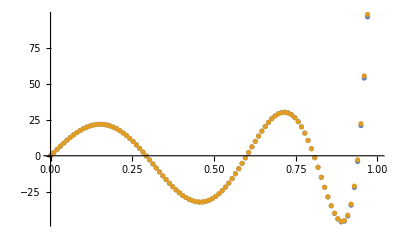

Power::infy: Infinite expression 1/0. encountered.

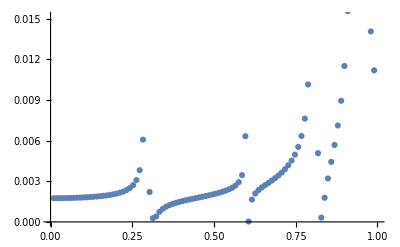

```mathematica
rg=fdsphgrid[100];
l=2;
n=4;
f =Wnl[n,l,rg]
g=D[Wnl[n,l,r],r]/.{r->rg}//N

fdOp=fdsphdiff[rg,1,2];
h=fdOp.f//N
ListPlot[{Transpose[{rg,g}],Transpose[{rg,h}]}]
ListPlot[{Transpose[{rg,Abs[g-h]/Abs[g]}]}]
```

```mathematica
rg=fdsphgrid[39];
l=18;
n=0;
f=(1+ⅈ)Wnl[n,l,r];
g=Abs[(1+ⅈ)divrdrWnl[n,l,r]]^2;
refEnergy=Integrate[g r^2,{r,0,1}];
fdOp=fdsphdiff[rg,1,2].DiagonalMatrix[rg];
fdg=Abs[fdOp.(f/.{r->rg})]^2;
wgts=fdsphintegral[rg,4,2];
fdEnergy=wgts.(fdg);
refEnergy//N
fdEnergy//N
Clear[l,n]
```

761.027

782.573

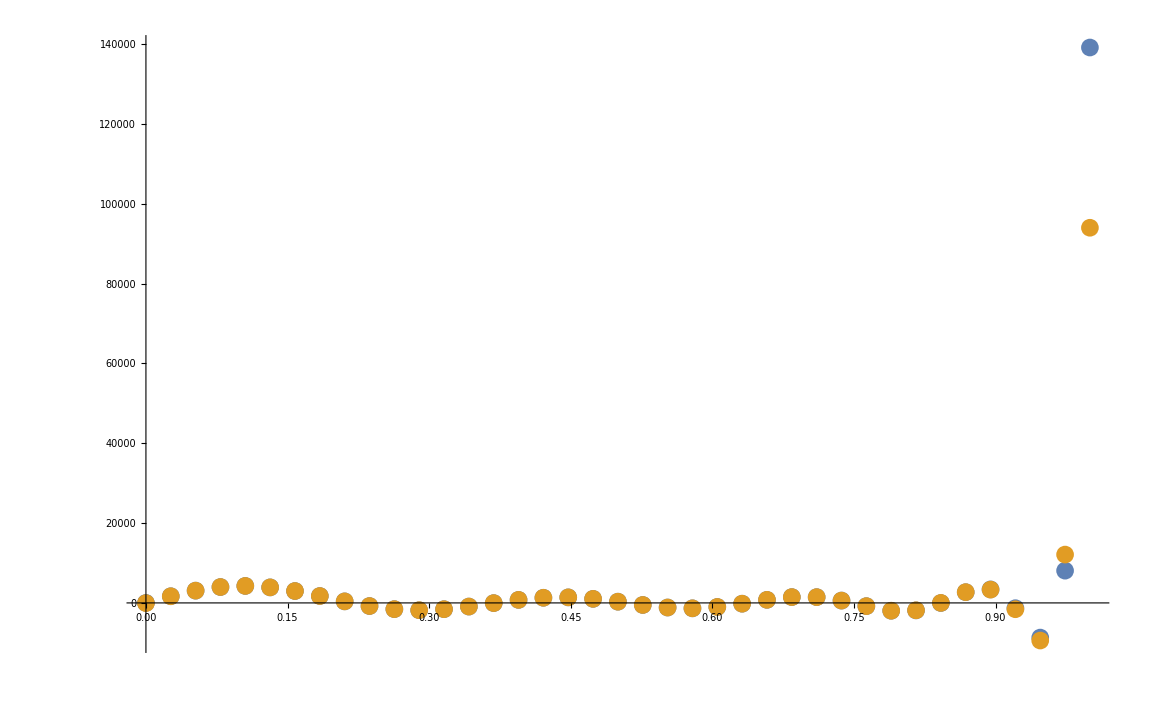

```mathematica
ListPlot[{Transpose[{rg,slaplWnl[9,1,rg]}],Transpose[{rg, fdOp.Wnl[9,1,rg]}]},PlotRange->All]
```